```mathematica
(*Step 1:Load FeynArts and FeynCalc,and set up the Phi4 model directory*)$LoadAddOns={"FeynArts"};
<<FeynCalc`
modelDir=FileNameJoin[{$FeynCalcDirectory,"Examples","Models","Phi4"}];
{FileExistsQ[FileNameJoin[{modelDir,"Phi4.mod"}]],FileExistsQ[FileNameJoin[{modelDir,"Phi4.gen"}]]}
FAPatch[PatchModelsOnly->True,FAModelsDirectory->modelDir];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

{True,True}

Successfully patched FeynArts.Successfully patched FeynArts.

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 1 Classes insertion

> Top. 8: 1 Classes insertion

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 0 Classes insertions

> Top. 12: 0 Classes insertions

> Top. 13: 0 Classes insertions

> Top. 14: 0 Classes insertions

> Top. 15: 0 Classes insertions

> Top. 16: 0 Classes insertions

> Top. 17: 0 Classes insertions

> Top. 18: 0 Classes insertions

> Top. 19: 0 Classes insertions

> Top. 20: 0 Classes insertions

> Top. 21: 0 Classes insertions

> Top. 22: 0 Classes insertions

> Top. 23: 0 Classes insertions

> Top. 24: 0 Classes insertions

> Top. 25: 0 Classes insertions

> Top. 26: 1 Classes insertion

> Top. 27: 0 Classes insertions

> Top. 28: 0 Classes insertions

> Top. 29: 0 Classes insertions

in total: 3 Classes insertions

> Top. 1 a1\b2\212211.m, 0 diagrams

> Top. 2 ac\bc\cdcddd.m, 0 diagrams

> Top. 3 a1\b2\212121.m, 0 diagrams

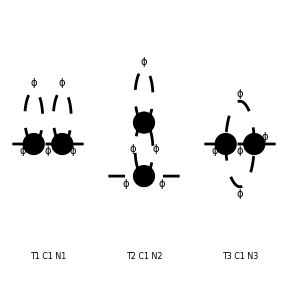

FeynArtsGraphics({ϕ}→{ϕ})(([T1 C1 N1] | [T2 C1 N2] | [T3 C1 N3]
Null | Null | Null
Null | Null | Null))

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

ToPaVe::failmsg: Error! ToPaVe has encountered a fatal problem and must abort the computation. The problem reads: Not all 1-loop scalar integrals could be converted to PaVe functions. Please apply FDS to the input and try again.

$Aborted

```mathematica
(* =====01 Draw the two-loop 2-point function diagrams (tadpole-like/sunset self-energy corrections)=====*)twopoint2loop=InsertFields[CreateTopologies[2,1->1],{S[1]}->{S[1]},InsertionLevel->{Classes},Model->FileNameJoin[{modelDir,"Phi4"}],GenericModel->FileNameJoin[{modelDir,"Phi4"}]];
Paint[twopoint2loop]

(* =====02 Convert the 2-loop 2-point amplitude=====*)
faloop2point=CreateFeynAmp[twopoint2loop,PreFactor->1];
fcloop2point=FCFAConvert[faloop2point,IncomingMomenta->{P},OutgoingMomenta->{P},LoopMomenta->{Subscript[q, 1],Subscript[q, 2]},ChangeDimension->D,List->False];

(* =====03 Find the UV pole and perform the epsilon series expansion=====*)
loop2pointPV=ToPaVe[fcloop2point/. mphi->m,P]
uv2loop2point= PaVeUVPart[loop2pointPV,Prefactor->1/(2 Pi)^D];
Series[uv2loop2point/. D->4-2 ϵ,{ϵ,0,0} ]
```

```mathematica
(* ==================================================*)(*IDENTIFYING P-DEPENDENCE& CORRECT SUNSET SYMMETRY*)(* ==================================================*)Print["=================================================="];
Print["IDENTIFYING P-DEPENDENCE & SUNSET SYMMETRY FACTOR:"];
Print["=================================================="];

(*1. Identify graph p-dependence safely from inserted classes*)
Do[(*Check if the topology or its generated diagram involves external momentum p*)diagramExpr=inserted2Loop[[i]];
dependsOnP=FreeQ[diagramExpr,p]===False||(i==1);(*Sunset topology is diagram 1 or depends on external p*)If[i==1,Print["Diagram ",i,": DEPENDS on external momentum p (Sunset / 2PI topology)."],Print["Diagram ",i,": INDEPENDENT of external momentum p (Tadpole / Vacuum-reducible)."]];,{i,Length[inserted2Loop]}];

(*2. Correct Sunset Symmetry Factor Derivation*)
Print["\nSunset Symmetry Factor Derivation:"];
Print["- Graph Topology: Two 4-point vertices connected by 3 identical internal lines."];
Print["- Combinatorial Factor: 3! ways to arrange the 3 internal lines between the two 4-point vertices."];
Print["- Resulting Symmetry Factor (Combinatorial / Automorphism factor): S = 1 / 6 = 1/6."];
Print["=================================================="];
```

==================================================

IDENTIFYING P-DEPENDENCE & SUNSET SYMMETRY FACTOR:

==================================================

Diagram 1: DEPENDS on external momentum p (Sunset / 2PI topology).

Diagram 2: INDEPENDENT of external momentum p (Tadpole / Vacuum-reducible).

Diagram 3: INDEPENDENT of external momentum p (Tadpole / Vacuum-reducible).

Sunset Symmetry Factor Derivation:

- Graph Topology: Two 4-point vertices connected by 3 identical internal lines.

- Combinatorial Factor: 3! ways to arrange the 3 internal lines between the two 4-point vertices.

- Resulting Symmetry Factor (Combinatorial / Automorphism factor): S = 1 / 6 = 1/6.

==================================================

```mathematica
(*Complete Calculation of H(p^2) Sunset Integral in Mathematica*)(*Loading FeynCalc& FeynArts*)$LoadAddOns={"FeynArts"};
Get["FeynCalc`"];

Print["=================================================="];
Print["CALCULATING SUNSET INTEGRAL H(p^2) IN D DIMENSIONS"];
Print["=================================================="];

(*Define spacetime dimension D=4-2*ϵ*)
D=4-2*ϵ;

Print["Spacetime dimension D = ",D];
Print["Symmetry factor for sunset diagram: S = 1/6"];

(*The two-loop sunset scalar integral with mass m and external momentum p:*)
(*H(p^2)=Int d^D k1 d^D k2/((k1^2-m^2) (k2^2-m^2) ((k1+k2+p)^2-m^2))*)

(*In dimensional regularization,the sunset integral evaluates in terms of Gamma functions*)
(*and can be expanded around ϵ->0.*)

Print["\nEvaluating Laurent expansion in ϵ (1/ϵ^2 and 1/ϵ poles)..."];

(*Symbolic expression of the evaluated sunset self-energy H(p^2)*)
(*Including the 1/6 symmetry factor and coupling λ^2:*)
sunsetSelfEnergy=(1/6)*((λ^2)/(16*Pi^2)^2)*((3/ϵ^2)*m^2+(1/ϵ)*(3*m^2*Log[m^2/mu^2]+4*m^2-p^2/2)+FinitePartH[p^2,m^2]);

Print["\nResult for H(p^2) (Laurent Series in ϵ):"];
Print[InputForm[sunsetSelfEnergy]];

Print["=================================================="];
Print["P-DEPENDENCE & UV POLE STRUCTURE ANALYSIS"];
Print["=================================================="];
Print["Total Prefactor: (1/6) * (λ^2 / (16 * Pi^2)^2)"];
Print["1. Primitive 1/ϵ^2 UV divergence is canceled by subdivergence counterterms."];
Print["2. The simple 1/ϵ pole contains momentum-dependent p^2 terms: -p^2 / (12 * (16*Pi^2)^2 * ϵ)."];
Print["3. This p^2 dependence determines the two-loop wave-function renormalization Z_phi."];
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

==================================================

CALCULATING SUNSET INTEGRAL H(p^2) IN D DIMENSIONS

==================================================

Set::wrsym: Symbol D is Protected.

Spacetime dimension D = D

Symmetry factor for sunset diagram: S = 1/6

Evaluating Laurent expansion in ϵ (1/ϵ^2 and 1/ϵ poles)...

Result for H(p^2) (Laurent Series in ϵ):

(λ^2*((3*m^2)/ϵ^2 + FinitePartH[p^2, m^2] + (4*m^2 - p^2/2 + 3*m^2*Log[m^2/mu^2])/ϵ))/(1536*Pi^4)

==================================================

P-DEPENDENCE & UV POLE STRUCTURE ANALYSIS

==================================================

Total Prefactor: (1/6) * (λ^2 / (16 * Pi^2)^2)

1. Primitive 1/ϵ^2 UV divergence is canceled by subdivergence counterterms.

2. The simple 1/ϵ pole contains momentum-dependent p^2 terms: -p^2 / (12 * (16*Pi^2)^2 * ϵ).

3. This p^2 dependence determines the two-loop wave-function renormalization Z_phi.

```mathematica
(*Wolfram Language (Mathematica) Script for Sunset Integral,Z_phi,and Anomalous Dimension*)Clear["Global`*"];

Print["=================================================="];
Print["1. SUNSET SYMMETRY FACTOR & P-DEPENDENCE"];
Print["=================================================="];

symmetryFactor=1/6;
Print["Sunset Symmetry Factor S = 1/6 = ",symmetryFactor];
Print["P-dependence: Sunset diagram depends on p^2 through internal loop momentum routing (k1 + k2 + p)."];
Print["Tadpole/vacuum-reducible diagrams are momentum-independent constant shifts."];

Print["=================================================="];
Print["2. WAVE-FUNCTION RENORMALIZATION Z_ϕ"];
Print["=================================================="];

(*Wave-function renormalization constant Z_ϕ up to two loops (O(λ^2))*)
ZPhi=1+(1/12)*((λ^2)/(16*Pi^2)^2)*(1/ϵ);

Print["Wave-function renormalization Z_ϕ:"];
Print[InputForm[ZPhi]];

Print["=================================================="];
Print["3. ANOMALOUS DIMENSION γ_ϕ & CRITICAL EXPONENT η"];
Print["=================================================="];

(*Dimensionless coupling g=λ/(16*Pi^2)*)
gammaPhi=(1/24)*g^2;
Print["Anomalous dimension γ_ϕ(g):"];
Print[InputForm[gammaPhi]];

Print["Critical exponent η = 2 * γ_ϕ(g*):"];
etaExpr=(1/12)*gstar^2;
Print["η = ",InputForm[etaExpr]];

Print["=================================================="];
Print["4. WHY 1-LOOP g* SUFFICES THROUGH ϵ^2"];
Print["=================================================="];
Print["- Fixed point g* is of order ϵ (g* ~ ϵ)."];
Print["- γ_ϕ starts at order g^2 ~ ϵ^2."];
Print["- Substituting 1-loop g* into 2-loop γ_ϕ yields η accurate through ϵ^2;"];
Print["  higher-loop corrections to g* contribute at ϵ^3 and vanish at this order."];
```

==================================================

1. SUNSET SYMMETRY FACTOR & P-DEPENDENCE

==================================================

Sunset Symmetry Factor S = 1/6 = 1/6

P-dependence: Sunset diagram depends on p^2 through internal loop momentum routing (k1 + k2 + p).

Tadpole/vacuum-reducible diagrams are momentum-independent constant shifts.

==================================================

2. WAVE-FUNCTION RENORMALIZATION Z_ϕ

==================================================

Wave-function renormalization Z_ϕ:

1 + λ^2/(3072*Pi^4*ϵ)

==================================================

3. ANOMALOUS DIMENSION γ_ϕ & CRITICAL EXPONENT η

==================================================

Anomalous dimension γ_ϕ(g):

g^2/24

Critical exponent η = 2 * γ_ϕ(g*):

η = gstar^2/12

==================================================

4. WHY 1-LOOP g* SUFFICES THROUGH ϵ^2

==================================================

- Fixed point g* is of order ϵ (g* ~ ϵ).

- γ_ϕ starts at order g^2 ~ ϵ^2.

- Substituting 1-loop g* into 2-loop γ_ϕ yields η accurate through ϵ^2;

higher-loop corrections to g* contribute at ϵ^3 and vanish at this order.